# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to no treatment BNT162b2-scaled peak (1.083940283) from Peeters et al. 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.083940283)*scalarsabove1
```

{1.08394,1.07626,1.06847,1.06058,1.05259,1.04451,1.03634,1.02811,1.01981,1.01147,1.00309,0.994685,0.986266,0.977845,0.969433,0.961038,0.952668,0.944332,0.936034,0.92778,0.919572,0.911411,0.9033,0.895237,0.887222,0.879251,0.871322,0.86343,0.855569,0.847736,0.839921,0.832118,0.824318,0.816475,0.808522,0.800444,0.792227,0.783856,0.775317,0.766599,0.757693,0.748593,0.7393,0.729823,0.720234,0.710645,0.701086,0.691582,0.682154,0.672816,0.663579,0.654449,0.645425,0.636505,0.627681,0.618942,0.610275,0.601663,0.593086,0.584519}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.08394,1.07626,1.06847,1.06058,1.05259,1.04451,1.03634,1.02811,1.01981,1.01147,1.00309,0.994685,0.986266,0.977845,0.969433,0.961038,0.952668,0.944332,0.936034,0.92778,0.919572,0.911411,0.9033,0.895237,0.887222,0.879251,0.871322,0.86343,0.855569,0.847736,0.839921,0.832118,0.824318,0.816475,0.808522,0.800444,0.792227,0.783856,0.775317,0.766599,0.757693,0.748593,0.7393,0.729823,0.720234,0.710645,0.701086,0.691582,0.682154,0.672816,0.663579,0.654449,0.645425,0.636505,0.627681,0.618942,0.610275,0.601663,0.593086,0.584519,0.582649,0.580787,0.578934,0.577088,0.575251,0.573422,0.571601,0.569788,0.567984,0.566187,0.564398,0.562618,0.560845,0.55908,0.557323,0.555574,0.553832,0.552099,0.550373,0.548654,0.546944,0.545241,0.543545,0.541857,0.540177,0.538504,0.536838,0.53518,0.533529,0.531886,0.53025,0.528621,0.527,0.525385,0.523778,0.522178,0.520585,0.519,0.517421,0.515849,0.514284,0.512727,0.511176,0.509632,0.508095,0.506565,0.505041,0.503525,0.502015,0.500511,0.499015,0.497525,0.496042,0.494565,0.493095,0.491632,0.490175,0.488724,0.48728,0.485843,0.484411,0.482987,0.481568,0.480156,0.47875,0.47735,0.475957,0.47457,0.473188,0.471814,0.470445,0.469082,0.467725,0.466375,0.46503,0.463691,0.462359,0.461032,0.459711,0.458396,0.457087,0.455784,0.454486,0.453195,0.451909,0.450628,0.449354,0.448085,0.446822,0.445564,0.444312,0.443065,0.441825,0.440589,0.439359,0.438135,0.436916,0.435702,0.434494,0.433291,0.432094,0.430902,0.429715,0.428533,0.427357,0.426186,0.42502,0.42386,0.422704,0.421554,0.420409,0.419269,0.418133,0.417003,0.415879,0.414759,0.413644,0.412534,0.411428,0.410328,0.409233,0.408143,0.407057,0.405976,0.4049,0.403829,0.402763,0.401701,0.400644,0.399592,0.398545,0.397502,0.396464,0.39543,0.394401,0.393377,0.392357,0.391341,0.390331,0.389324,0.388322,0.387325,0.386332,0.385344,0.384359,0.38338,0.382404,0.381433,0.380467,0.379504,0.378546,0.377592,0.376642,0.375697,0.374756,0.373819,0.372886,0.371957,0.371033,0.370112,0.369196,0.368284,0.367375,0.366471,0.365571,0.364675,0.363783,0.362894,0.36201,0.36113,0.360254,0.359381,0.358512,0.357648,0.356787,0.35593,0.355076,0.354227,0.353381,0.352539,0.351701,0.350867,0.350036,0.349209,0.348385,0.347566,0.34675,0.345937,0.345128,0.344323,0.343522,0.342724,0.341929,0.341138,0.340351,0.339567,0.338786,0.338009,0.337236,0.336466,0.335699,0.334936,0.334176,0.333419,0.332666,0.331916,0.33117,0.330427,0.329687,0.32895,0.328217,0.327487,0.326761,0.326037,0.325317,0.3246,0.323886,0.323175,0.322468,0.321763,0.321062,0.320364,0.319669,0.318977,0.318288,0.317602,0.316919,0.31624,0.315563,0.314889,0.314219,0.313551,0.312886,0.312224,0.311565,0.31091,0.310257,0.309607,0.308959,0.308315,0.307674,0.307035,0.306399,0.305766,0.305136,0.304509,0.303884,0.303263,0.302644,0.302028,0.301414,0.300803,0.300195,0.29959,0.298987,0.298387,0.29779,0.297196,0.296604,0.296014,0.295428,0.294843,0.294262,0.293683,0.293107,0.292533,0.291962,0.291393,0.290827,0.290263,0.289702,0.289143,0.288587,0.288034,0.287482,0.286934,0.286387,0.285843,0.285302,0.284763,0.284226,0.283692,0.28316,0.282631,0.282103,0.281579,0.281056,0.280536,0.280018,0.279503,0.278989,0.278478,0.27797,0.277463,0.276959,0.276457,0.275957,0.27546,0.274965,0.274471,0.273981,0.273492,0.273005,0.272521,0.272039,0.271559,0.271081,0.270605,0.270131,0.26966,0.26919,0.268723,0.268258,0.267794,0.267333,0.266874,0.266417,0.265962,0.265509,0.265058,0.264609,0.264162,0.263717,0.263274,0.262833,0.262394,0.261957,0.261522,0.261088,0.260657,0.260228,0.2598,0.259374,0.258951,0.258529,0.258109,0.257691,0.257275,0.25686,0.256448,0.256037,0.255628,0.255221,0.254816,0.254412,0.254011,0.253611,0.253213,0.252817,0.252422,0.252029,0.251638,0.251249,0.250861,0.250476,0.250091,0.249709,0.249328,0.248949,0.248572,0.248196,0.247822,0.24745,0.247079,0.24671,0.246343,0.245977,0.245613,0.245251,0.24489,0.244531,0.244173,0.243817,0.243462,0.243109,0.242758,0.242408,0.24206,0.241713,0.241368,0.241025,0.240682,0.240342,0.240003,0.239665,0.239329,0.238995,0.238662,0.23833,0.238,0.237671,0.237344,0.237019,0.236694,0.236372,0.23605,0.23573,0.235412,0.235095,0.234779,0.234465,0.234152,0.23384,0.23353,0.233221,0.232914,0.232608,0.232303,0.232,0.231698,0.231398,0.231098,0.2308,0.230504,0.230209,0.229915,0.229622,0.229331,0.229041,0.228752,0.228464,0.228178,0.227893,0.22761,0.227327,0.227046,0.226766,0.226488,0.22621,0.225934,0.225659,0.225385,0.225113,0.224842,0.224571,0.224303,0.224035,0.223768,0.223503,0.223239,0.222976,0.222714,0.222454,0.222194,0.221936,0.221679,0.221423,0.221168,0.220914,0.220662,0.22041,0.22016,0.21991,0.219662,0.219415,0.219169,0.218924,0.218681,0.218438,0.218196,0.217956,0.217716,0.217478,0.217241,0.217004,0.216769,0.216535,0.216302,0.21607,0.215839,0.215609,0.21538,0.215152,0.214925,0.214699,0.214474,0.21425,0.214027,0.213805,0.213584,0.213364,0.213145,0.212927,0.21271,0.212494,0.212279,0.212064,0.211851,0.211639,0.211428,0.211217,0.211008,0.210799,0.210592,0.210385,0.210179,0.209974,0.20977,0.209567,0.209365,0.209164,0.208964,0.208764,0.208566,0.208368,0.208171,0.207975,0.20778,0.207586,0.207393,0.2072,0.207009,0.206818,0.206628,0.206439,0.206251,0.206063,0.205877,0.205691,0.205506,0.205322,0.205139,0.204957,0.204775,0.204594,0.204414,0.204235,0.204057,0.203879,0.203702,0.203526,0.203351,0.203176,0.203003,0.20283,0.202658,0.202486,0.202316,0.202146,0.201977,0.201808,0.201641,0.201474,0.201308,0.201142,0.200978,0.200814,0.200651,0.200488,0.200326,0.200165,0.200005,0.199845,0.199687,0.199528,0.199371,0.199214,0.199058,0.198903,0.198748,0.198594,0.198441,0.198288,0.198136,0.197985,0.197834,0.197684,0.197535,0.197387,0.197239,0.197091,0.196945,0.196799,0.196653,0.196509,0.196365,0.196221,0.196079,0.195936,0.195795,0.195654,0.195514,0.195374,0.195235,0.195097,0.194959,0.194822,0.194685,0.19455,0.194414,0.19428,0.194145,0.194012,0.193879,0.193747,0.193615,0.193484,0.193353,0.193223,0.193094,0.192965,0.192837,0.192709,0.192582,0.192455,0.192329,0.192204,0.192079,0.191955,0.191831,0.191708,0.191585,0.191463,0.191341,0.19122,0.1911,0.19098,0.19086,0.190741,0.190623,0.190505,0.190388,0.190271,0.190155,0.190039,0.189924,0.189809,0.189695,0.189581,0.189468,0.189355,0.189243,0.189131,0.18902,0.188909,0.188799,0.188689,0.18858,0.188471,0.188363,0.188255,0.188148,0.188041,0.187935,0.187829,0.187723,0.187619,0.187514,0.18741,0.187306,0.187203,0.187101,0.186999,0.186897,0.186796,0.186695,0.186594,0.186494,0.186395,0.186296,0.186197,0.186099,0.186001,0.185904,0.185807,0.185711,0.185615,0.185519,0.185424,0.185329,0.185235,0.185141,0.185048,0.184955,0.184862,0.18477,0.184678,0.184587,0.184496,0.184405,0.184315,0.184225,0.184136,0.184047,0.183958,0.18387,0.183782,0.183695,0.183608,0.183521,0.183435,0.183349,0.183264,0.183178,0.183094,0.183009,0.182925,0.182842,0.182759,0.182676,0.182593,0.182511,0.182429,0.182348,0.182267,0.182186,0.182106,0.182026,0.181946,0.181867,0.181788,0.18171,0.181631,0.181554,0.181476,0.181399,0.181322,0.181246,0.18117,0.181094,0.181018,0.180943,0.180868,0.180794,0.18072,0.180646,0.180573,0.180499,0.180427,0.180354,0.180282,0.18021,0.180139,0.180067,0.179997,0.179926,0.179856,0.179786,0.179716,0.179647,0.179578,0.179509,0.179441,0.179373,0.179305,0.179237,0.17917,0.179103,0.179037,0.17897,0.178904,0.178839,0.178773,0.178708,0.178643,0.178579,0.178514,0.17845,0.178387,0.178323,0.17826,0.178197,0.178135,0.178072,0.17801,0.177949,0.177887,0.177826,0.177765,0.177705,0.177644,0.177584,0.177524,0.177465,0.177405,0.177346,0.177287,0.177229,0.177171,0.177113,0.177055,0.176997,0.17694,0.176883,0.176827,0.17677,0.176714,0.176658,0.176602,0.176547,0.176491,0.176437,0.176382,0.176327,0.176273,0.176219,0.176165,0.176112,0.176058,0.176005,0.175953,0.1759,0.175848,0.175796,0.175744,0.175692,0.175641,0.175589,0.175538,0.175488,0.175437,0.175387,0.175337,0.175287,0.175237,0.175188,0.175139,0.17509,0.175041,0.174993,0.174944,0.174896,0.174848,0.174801,0.174753,0.174706,0.174659,0.174612,0.174565,0.174519,0.174473,0.174427,0.174381,0.174335,0.17429,0.174245,0.1742,0.174155,0.174111,0.174066,0.174022,0.173978,0.173934,0.173891,0.173847,0.173804,0.173761,0.173718,0.173675,0.173633,0.173591,0.173549,0.173507,0.173465,0.173424,0.173382,0.173341,0.1733,0.173259,0.173219,0.173178,0.173138,0.173098,0.173058,0.173018,0.172979,0.17294,0.1729,0.172861,0.172823,0.172784,0.172745,0.172707,0.172669,0.172631,0.172593,0.172556,0.172518,0.172481,0.172444,0.172407,0.17237,0.172333,0.172297,0.17226,0.172224,0.172188,0.172152,0.172117,0.172081,0.172046,0.172011,0.171976,0.171941,0.171906,0.171871,0.171837,0.171803,0.171769,0.171735,0.171701,0.171667,0.171634,0.1716,0.171567,0.171534,0.171501,0.171468,0.171436,0.171403,0.171371,0.171339,0.171307,0.171275,0.171243,0.171211,0.17118,0.171148,0.171117,0.171086,0.171055,0.171024,0.170994,0.170963,0.170933,0.170903,0.170873,0.170843,0.170813,0.170783,0.170753,0.170724,0.170695,0.170665,0.170636,0.170607,0.170579,0.17055,0.170521,0.170493,0.170465,0.170437,0.170408,0.170381,0.170353,0.170325,0.170298,0.17027,0.170243,0.170216,0.170189,0.170162,0.170135,0.170108,0.170082,0.170055,0.170029,0.170003,0.169976,0.16995,0.169925,0.169899,0.169873,0.169848,0.169822,0.169797,0.169772,0.169747,0.169722,0.169697,0.169672,0.169647,0.169623,0.169598,0.169574,0.16955,0.169526,0.169502,0.169478,0.169454,0.169431,0.169407,0.169383,0.16936,0.169337,0.169314,0.169291,0.169268,0.169245,0.169222,0.1692,0.169177,0.169155,0.169132,0.16911,0.169088,0.169066,0.169044,0.169022,0.169,0.168979,0.168957,0.168936,0.168914,0.168893,0.168872,0.168851,0.16883,0.168809,0.168788,0.168767,0.168747,0.168726,0.168706,0.168685,0.168665,0.168645,0.168625,0.168605,0.168585,0.168565,0.168546,0.168526,0.168506,0.168487,0.168468,0.168448,0.168429,0.16841,0.168391,0.168372,0.168353,0.168334,0.168316,0.168297,0.168279,0.16826,0.168242,0.168223,0.168205,0.168187,0.168169,0.168151,0.168133,0.168115,0.168098,0.16808,0.168063,0.168045,0.168028,0.16801,0.167993,0.167976,0.167959,0.167942,0.167925,0.167908,0.167891,0.167875,0.167858,0.167841,0.167825,0.167808,0.167792,0.167776,0.16776,0.167743,0.167727,0.167711,0.167695,0.16768,0.167664,0.167648,0.167633,0.167617,0.167601,0.167586,0.167571,0.167555,0.16754,0.167525,0.16751,0.167495,0.16748,0.167465,0.16745,0.167435,0.167421,0.167406,0.167392,0.167377,0.167363,0.167348,0.167334,0.16732,0.167306,0.167291,0.167277,0.167263,0.167249,0.167236,0.167222,0.167208,0.167194,0.167181,0.167167,0.167154,0.16714,0.167127,0.167114,0.1671,0.167087,0.167074,0.167061,0.167048,0.167035,0.167022,0.167009,0.166996,0.166984,0.166971,0.166958,0.166946,0.166933,0.166921,0.166908,0.166896,0.166884,0.166872,0.166859,0.166847,0.166835,0.166823,0.166811,0.166799,0.166787,0.166776,0.166764,0.166752,0.16674,0.166729,0.166717,0.166706,0.166694,0.166683,0.166672,0.16666,0.166649,0.166638,0.166627,0.166616,0.166605,0.166594,0.166583,0.166572,0.166561,0.16655,0.166539,0.166529,0.166518,0.166507,0.166497,0.166486,0.166476,0.166466,0.166455,0.166445,0.166435,0.166424,0.166414,0.166404,0.166394,0.166384,0.166374,0.166364,0.166354,0.166344,0.166334,0.166324,0.166315,0.166305,0.166295,0.166286,0.166276,0.166267,0.166257,0.166248,0.166238,0.166229,0.16622,0.16621,0.166201,0.166192,0.166183,0.166174,0.166164,0.166155,0.166146,0.166137,0.166129,0.16612,0.166111,0.166102,0.166093,0.166085,0.166076,0.166067,0.166059,0.16605,0.166042,0.166033,0.166025,0.166016,0.166008,0.165999,0.165991,0.165983,0.165975,0.165967,0.165958,0.16595,0.165942,0.165934,0.165926,0.165918,0.16591,0.165902,0.165894,0.165887,0.165879,0.165871,0.165863,0.165856,0.165848,0.16584,0.165833,0.165825,0.165818,0.16581,0.165803,0.165795,0.165788,0.16578,0.165773,0.165766,0.165759,0.165751,0.165744,0.165737,0.16573,0.165723,0.165716,0.165709,0.165702,0.165695,0.165688,0.165681,0.165674,0.165667,0.16566,0.165653,0.165647,0.16564,0.165633,0.165627,0.16562,0.165613,0.165607,0.1656,0.165594,0.165587,0.165581,0.165574,0.165568,0.165561,0.165555,0.165549,0.165543,0.165536,0.16553,0.165524,0.165518,0.165511,0.165505,0.165499,0.165493,0.165487,0.165481,0.165475,0.165469,0.165463,0.165457,0.165451,0.165446,0.16544,0.165434,0.165428,0.165422,0.165417,0.165411,0.165405,0.1654,0.165394,0.165388,0.165383,0.165377,0.165372,0.165366,0.165361,0.165355,0.16535,0.165344,0.165339,0.165334,0.165328,0.165323,0.165318,0.165312,0.165307,0.165302,0.165297,0.165292,0.165286,0.165281,0.165276,0.165271,0.165266,0.165261,0.165256,0.165251,0.165246,0.165241,0.165236,0.165231,0.165226,0.165221,0.165217,0.165212,0.165207,0.165202,0.165197,0.165193,0.165188,0.165183,0.165179,0.165174,0.165169,0.165165,0.16516,0.165156,0.165151,0.165147,0.165142,0.165138,0.165133,0.165129,0.165124,0.16512,0.165115,0.165111,0.165107,0.165102,0.165098,0.165094,0.165089,0.165085,0.165081,0.165077,0.165073,0.165068,0.165064,0.16506,0.165056,0.165052,0.165048,0.165044,0.16504,0.165036,0.165032,0.165028,0.165024,0.16502,0.165016,0.165012,0.165008,0.165004,0.165,0.164996,0.164992,0.164989,0.164985,0.164981,0.164977,0.164974,0.16497,0.164966,0.164962,0.164959,0.164955,0.164951,0.164948,0.164944,0.16494,0.164937,0.164933,0.16493,0.164926,0.164923,0.164919,0.164916,0.164912,0.164909,0.164905,0.164902,0.164898,0.164895,0.164892,0.164888,0.164885,0.164882,0.164878,0.164875,0.164872,0.164868,0.164865,0.164862,0.164859,0.164855,0.164852,0.164849,0.164846,0.164843,0.164839,0.164836,0.164833,0.16483,0.164827,0.164824,0.164821,0.164818,0.164815,0.164812,0.164809,0.164806,0.164803,0.1648,0.164797,0.164794,0.164791,0.164788,0.164785,0.164782,0.164779,0.164776,0.164773,0.164771,0.164768,0.164765,0.164762,0.164759,0.164757,0.164754,0.164751,0.164748,0.164746,0.164743,0.16474,0.164737,0.164735,0.164732,0.164729,0.164727,0.164724,0.164722,0.164719,0.164716,0.164714,0.164711,0.164709,0.164706,0.164703,0.164701,0.164698,0.164696,0.164693,0.164691,0.164688,0.164686,0.164683,0.164681,0.164679,0.164676,0.164674,0.164671,0.164669,0.164667,0.164664,0.164662,0.164659,0.164657,0.164655,0.164652,0.16465,0.164648,0.164646,0.164643,0.164641,0.164639,0.164637,0.164634,0.164632,0.16463,0.164628,0.164625,0.164623,0.164621,0.164619,0.164617,0.164615,0.164612,0.16461,0.164608,0.164606,0.164604,0.164602,0.1646,0.164598,0.164596,0.164594,0.164592,0.16459,0.164588,0.164585,0.164583,0.164581,0.164579,0.164578,0.164576,0.164574,0.164572,0.16457,0.164568,0.164566,0.164564,0.164562,0.16456,0.164558,0.164556,0.164554,0.164552,0.164551,0.164549,0.164547,0.164545,0.164543,0.164541,0.16454,0.164538,0.164536,0.164534,0.164532,0.164531,0.164529,0.164527,0.164525,0.164524,0.164522,0.16452,0.164518,0.164517,0.164515,0.164513,0.164512,0.16451,0.164508,0.164507,0.164505,0.164503,0.164502,0.1645,0.164498,0.164497,0.164495,0.164494,0.164492,0.16449,0.164489,0.164487,0.164486,0.164484,0.164482,0.164481,0.164479,0.164478,0.164476,0.164475,0.164473,0.164472,0.16447,0.164469,0.164467,0.164466,0.164464,0.164463,0.164461,0.16446,0.164458,0.164457,0.164456,0.164454,0.164453,0.164451,0.16445,0.164448,0.164447,0.164446,0.164444,0.164443,0.164442,0.16444,0.164439,0.164437,0.164436,0.164435,0.164433,0.164432,0.164431,0.164429,0.164428,0.164427,0.164425,0.164424,0.164423,0.164422,0.16442,0.164419,0.164418,0.164417,0.164415,0.164414,0.164413,0.164412,0.16441,0.164409,0.164408,0.164407,0.164405,0.164404,0.164403,0.164402,0.164401,0.164399,0.164398,0.164397,0.164396,0.164395,0.164394,0.164392,0.164391,0.16439,0.164389,0.164388,0.164387,0.164386,0.164384,0.164383,0.164382,0.164381,0.16438,0.164379,0.164378,0.164377,0.164376,0.164375,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164342,0.164341,0.16434,0.164339,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164332,0.164332,0.164331,0.16433,0.164329,0.164328,0.164327,0.164326,0.164326,0.164325,0.164324,0.164323,0.164322,0.164321,0.16432,0.16432,0.164319,0.164318,0.164317,0.164316,0.164316,0.164315,0.164314,0.164313,0.164312,0.164312,0.164311,0.16431,0.164309,0.164308,0.164308,0.164307,0.164306,0.164305,0.164304,0.164304,0.164303,0.164302,0.164301,0.164301,0.1643,0.164299,0.164299,0.164298,0.164297,0.164296,0.164296,0.164295,0.164294,0.164293,0.164293,0.164292,0.164291,0.164291,0.16429,0.164289,0.164289,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164284,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164278,0.164278,0.164277,0.164277,0.164276,0.164275,0.164275,0.164274,0.164273,0.164273,0.164272,0.164272,0.164271,0.16427,0.16427,0.164269,0.164269,0.164268,0.164267,0.164267,0.164266,0.164266,0.164265,0.164264,0.164264,0.164263,0.164263,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164259,0.164258,0.164258,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164235,0.164234,0.164234,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.164231,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164228,0.164227,0.164227,0.164226,0.164226,0.164226,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.16422,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164217,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.445564

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

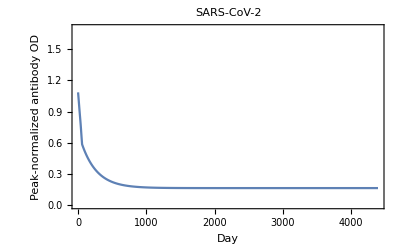

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

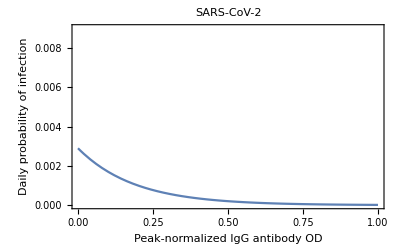

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999991,0.999981,0.99997,0.99996,0.999949,0.999937,0.999925,0.999912,0.999899,0.999885,0.99987,0.999855,0.999839,0.999822,0.999805,0.999787,0.999768,0.999748,0.999727,0.999705,0.999683,0.999659,0.999634,0.999608,0.999582,0.999553,0.999524,0.999494,0.999462,0.999429,0.999394,0.999358,0.99932,0.999281,0.99924,0.999197,0.999153,0.999106,0.999057,0.999006,0.998952,0.998895,0.998835,0.998773,0.998707,0.998637,0.998564,0.998488,0.998407,0.998322,0.998233,0.99814,0.998042,0.997939,0.997832,0.99772,0.997602,0.997479,0.99735,0.997219,0.997088,0.996955,0.996821,0.996686,0.996549,0.996411,0.996272,0.996131,0.995989,0.995846,0.995701,0.995555,0.995408,0.995259,0.995109,0.994957,0.994804,0.99465,0.994495,0.994338,0.994179,0.994019,0.993858,0.993695,0.993531,0.993366,0.993199,0.99303,0.99286,0.992689,0.992516,0.992342,0.992166,0.991989,0.99181,0.99163,0.991448,0.991265,0.99108,0.990894,0.990706,0.990517,0.990326,0.990134,0.98994,0.989745,0.989548,0.98935,0.98915,0.988948,0.988745,0.98854,0.988334,0.988126,0.987917,0.987705,0.987493,0.987279,0.987063,0.986845,0.986626,0.986406,0.986184,0.98596,0.985734,0.985507,0.985278,0.985048,0.984816,0.984582,0.984347,0.98411,0.983871,0.983631,0.983389,0.983146,0.9829,0.982654,0.982405,0.982155,0.981903,0.981649,0.981394,0.981137,0.980878,0.980618,0.980356,0.980092,0.979827,0.979559,0.97929,0.97902,0.978748,0.978474,0.978198,0.97792,0.977641,0.97736,0.977078,0.976794,0.976508,0.97622,0.97593,0.975639,0.975346,0.975051,0.974755,0.974457,0.974157,0.973855,0.973552,0.973247,0.97294,0.972631,0.972321,0.972009,0.971695,0.971379,0.971062,0.970743,0.970422,0.970099,0.969775,0.969449,0.969121,0.968791,0.96846,0.968127,0.967792,0.967455,0.967117,0.966777,0.966435,0.966091,0.965746,0.965398,0.965049,0.964699,0.964346,0.963992,0.963636,0.963278,0.962919,0.962558,0.962195,0.96183,0.961463,0.961095,0.960725,0.960354,0.95998,0.959605,0.959228,0.958849,0.958469,0.958087,0.957703,0.957317,0.95693,0.95654,0.95615,0.955757,0.955363,0.954966,0.954569,0.954169,0.953768,0.953365,0.95296,0.952554,0.952146,0.951736,0.951324,0.950911,0.950496,0.950079,0.949661,0.949241,0.948819,0.948396,0.94797,0.947543,0.947115,0.946685,0.946253,0.945819,0.945384,0.944947,0.944508,0.944068,0.943626,0.943182,0.942737,0.94229,0.941841,0.941391,0.940939,0.940486,0.94003,0.939573,0.939115,0.938655,0.938193,0.93773,0.937265,0.936798,0.93633,0.93586,0.935388,0.934915,0.934441,0.933965,0.933487,0.933007,0.932526,0.932044,0.931559,0.931074,0.930586,0.930097,0.929607,0.929115,0.928621,0.928126,0.92763,0.927131,0.926632,0.92613,0.925628,0.925123,0.924617,0.92411,0.923601,0.923091,0.922579,0.922065,0.921551,0.921034,0.920516,0.919997,0.919476,0.918954,0.91843,0.917905,0.917379,0.91685,0.916321,0.91579,0.915258,0.914724,0.914188,0.913652,0.913114,0.912574,0.912033,0.911491,0.910947,0.910402,0.909856,0.909308,0.908759,0.908208,0.907656,0.907103,0.906548,0.905992,0.905435,0.904876,0.904316,0.903755,0.903192,0.902628,0.902063,0.901496,0.900928,0.900359,0.899788,0.899217,0.898643,0.898069,0.897494,0.896917,0.896339,0.895759,0.895179,0.894597,0.894014,0.893429,0.892844,0.892257,0.891669,0.89108,0.89049,0.889898,0.889305,0.888711,0.888116,0.88752,0.886923,0.886324,0.885724,0.885123,0.884521,0.883918,0.883314,0.882708,0.882102,0.881494,0.880885,0.880276,0.879665,0.879053,0.878439,0.877825,0.87721,0.876594,0.875976,0.875358,0.874738,0.874118,0.873496,0.872873,0.87225,0.871625,0.870999,0.870373,0.869745,0.869116,0.868487,0.867856,0.867225,0.866592,0.865958,0.865324,0.864688,0.864052,0.863415,0.862776,0.862137,0.861497,0.860856,0.860214,0.859571,0.858927,0.858283,0.857637,0.856991,0.856343,0.855695,0.855046,0.854396,0.853745,0.853094,0.852441,0.851788,0.851134,0.850479,0.849823,0.849167,0.848509,0.847851,0.847192,0.846532,0.845872,0.845211,0.844549,0.843886,0.843222,0.842558,0.841893,0.841227,0.84056,0.839893,0.839225,0.838556,0.837887,0.837217,0.836546,0.835874,0.835202,0.834529,0.833855,0.833181,0.832506,0.831831,0.831154,0.830477,0.8298,0.829122,0.828443,0.827763,0.827083,0.826403,0.825721,0.82504,0.824357,0.823674,0.82299,0.822306,0.821621,0.820936,0.82025,0.819564,0.818876,0.818189,0.817501,0.816812,0.816123,0.815433,0.814743,0.814052,0.813361,0.812669,0.811977,0.811284,0.810591,0.809897,0.809203,0.808508,0.807813,0.807117,0.806421,0.805725,0.805028,0.80433,0.803632,0.802934,0.802236,0.801536,0.800837,0.800137,0.799437,0.798736,0.798035,0.797333,0.796631,0.795929,0.795226,0.794523,0.79382,0.793116,0.792412,0.791708,0.791003,0.790298,0.789593,0.788887,0.788181,0.787474,0.786768,0.786061,0.785353,0.784646,0.783938,0.78323,0.782521,0.781812,0.781103,0.780394,0.779685,0.778975,0.778265,0.777554,0.776844,0.776133,0.775422,0.774711,0.773999,0.773287,0.772576,0.771863,0.771151,0.770439,0.769726,0.769013,0.7683,0.767586,0.766873,0.766159,0.765445,0.764731,0.764017,0.763303,0.762589,0.761874,0.761159,0.760444,0.759729,0.759014,0.758299,0.757583,0.756868,0.756152,0.755436,0.75472,0.754005,0.753288,0.752572,0.751856,0.75114,0.750423,0.749707,0.74899,0.748274,0.747557,0.74684,0.746123,0.745407,0.74469,0.743973,0.743256,0.742539,0.741822,0.741105,0.740387,0.73967,0.738953,0.738236,0.737519,0.736802,0.736084,0.735367,0.73465,0.733933,0.733216,0.732499,0.731782,0.731064,0.730347,0.72963,0.728913,0.728197,0.72748,0.726763,0.726046,0.725329,0.724613,0.723896,0.723179,0.722463,0.721746,0.72103,0.720314,0.719598,0.718881,0.718165,0.71745,0.716734,0.716018,0.715302,0.714587,0.713871,0.713156,0.712441,0.711726,0.711011,0.710296,0.709581,0.708867,0.708152,0.707438,0.706724,0.70601,0.705296,0.704582,0.703869,0.703156,0.702442,0.701729,0.701016,0.700304,0.699591,0.698879,0.698166,0.697454,0.696743,0.696031,0.695319,0.694608,0.693897,0.693186,0.692475,0.691765,0.691055,0.690345,0.689635,0.688925,0.688216,0.687506,0.686798,0.686089,0.68538,0.684672,0.683964,0.683256,0.682548,0.681841,0.681134,0.680427,0.679721,0.679014,0.678308,0.677602,0.676897,0.676191,0.675486,0.674782,0.674077,0.673373,0.672669,0.671965,0.671262,0.670559,0.669856,0.669153,0.668451,0.667749,0.667047,0.666346,0.665645,0.664944,0.664244,0.663543,0.662843,0.662144,0.661445,0.660746,0.660047,0.659349,0.658651,0.657953,0.657256,0.656559,0.655862,0.655166,0.65447,0.653774,0.653079,0.652384,0.651689,0.650995,0.650301,0.649607,0.648914,0.648221,0.647528,0.646836,0.646144,0.645453,0.644762,0.644071,0.643381,0.64269,0.642001,0.641312,0.640623,0.639934,0.639246,0.638558,0.637871,0.637184,0.636497,0.635811,0.635125,0.634439,0.633754,0.633069,0.632385,0.631701,0.631018,0.630335,0.629652,0.62897,0.628288,0.627606,0.626925,0.626244,0.625564,0.624884,0.624205,0.623526,0.622847,0.622169,0.621491,0.620814,0.620137,0.61946,0.618784,0.618108,0.617433,0.616758,0.616084,0.61541,0.614736,0.614063,0.613391,0.612718,0.612047,0.611375,0.610704,0.610034,0.609364,0.608694,0.608025,0.607357,0.606688,0.606021,0.605353,0.604686,0.60402,0.603354,0.602689,0.602024,0.601359,0.600695,0.600031,0.599368,0.598705,0.598043,0.597381,0.59672,0.596059,0.595399,0.594739,0.594079,0.59342,0.592762,0.592104,0.591446,0.590789,0.590133,0.589477,0.588821,0.588166,0.587511,0.586857,0.586204,0.58555,0.584898,0.584245,0.583594,0.582942,0.582292,0.581641,0.580992,0.580342,0.579694,0.579045,0.578398,0.57775,0.577104,0.576457,0.575812,0.575166,0.574521,0.573877,0.573233,0.57259,0.571947,0.571305,0.570663,0.570022,0.569381,0.568741,0.568101,0.567462,0.566824,0.566185,0.565548,0.564911,0.564274,0.563638,0.563002,0.562367,0.561733,0.561098,0.560465,0.559832,0.559199,0.558567,0.557936,0.557305,0.556675,0.556045,0.555415,0.554787,0.554158,0.55353,0.552903,0.552276,0.55165,0.551025,0.550399,0.549775,0.549151,0.548527,0.547904,0.547282,0.54666,0.546038,0.545417,0.544797,0.544177,0.543558,0.542939,0.542321,0.541703,0.541086,0.540469,0.539853,0.539238,0.538623,0.538008,0.537394,0.536781,0.536168,0.535556,0.534944,0.534333,0.533722,0.533112,0.532502,0.531893,0.531285,0.530677,0.530069,0.529462,0.528856,0.52825,0.527645,0.52704,0.526436,0.525832,0.525229,0.524627,0.524025,0.523423,0.522823,0.522222,0.521622,0.521023,0.520424,0.519826,0.519229,0.518632,0.518035,0.517439,0.516844,0.516249,0.515655,0.515061,0.514468,0.513875,0.513283,0.512692,0.512101,0.51151,0.51092,0.510331,0.509742,0.509154,0.508566,0.507979,0.507393,0.506807,0.506221,0.505636,0.505052,0.504468,0.503885,0.503302,0.50272,0.502139,0.501558,0.500977,0.500397,0.499818,0.499239,0.498661,0.498083,0.497506,0.49693,0.496354,0.495778,0.495203,0.494629,0.494055,0.493482,0.49291,0.492337,0.491766,0.491195,0.490624,0.490055,0.489485,0.488917,0.488348,0.487781,0.487214,0.486647,0.486081,0.485516,0.484951,0.484387,0.483823,0.48326,0.482697,0.482135,0.481573,0.481013,0.480452,0.479892,0.479333,0.478774,0.478216,0.477659,0.477101,0.476545,0.475989,0.475434,0.474879,0.474325,0.473771,0.473218,0.472665,0.472113,0.471562,0.471011,0.47046,0.469911,0.469361,0.468813,0.468264,0.467717,0.46717,0.466623,0.466077,0.465532,0.464987,0.464443,0.463899,0.463356,0.462814,0.462272,0.46173,0.461189,0.460649,0.460109,0.45957,0.459031,0.458493,0.457955,0.457418,0.456882,0.456346,0.455811,0.455276,0.454742,0.454208,0.453675,0.453142,0.45261,0.452078,0.451548,0.451017,0.450487,0.449958,0.449429,0.448901,0.448373,0.447846,0.44732,0.446794,0.446268,0.445744,0.445219,0.444695,0.444172,0.443649,0.443127,0.442606,0.442085,0.441564,0.441044,0.440525,0.440006,0.439488,0.43897,0.438453,0.437936,0.43742,0.436904,0.436389,0.435875,0.435361,0.434848,0.434335,0.433823,0.433311,0.4328,0.432289,0.431779,0.431269,0.43076,0.430252,0.429744,0.429237,0.42873,0.428223,0.427718,0.427212,0.426708,0.426204,0.4257,0.425197,0.424694,0.424192,0.423691,0.42319,0.42269,0.42219,0.421691,0.421192,0.420694,0.420196,0.419699,0.419202,0.418706,0.418211,0.417716,0.417221,0.416728,0.416234,0.415741,0.415249,0.414757,0.414266,0.413775,0.413285,0.412796,0.412306,0.411818,0.41133,0.410842,0.410355,0.409869,0.409383,0.408898,0.408413,0.407929,0.407445,0.406962,0.406479,0.405997,0.405515,0.405034,0.404553,0.404073,0.403594,0.403115,0.402636,0.402158,0.401681,0.401204,0.400727,0.400252,0.399776,0.399301,0.398827,0.398353,0.39788,0.397407,0.396935,0.396463,0.395992,0.395522,0.395052,0.394582,0.394113,0.393644,0.393176,0.392709,0.392242,0.391775,0.391309,0.390844,0.390379,0.389914,0.389451,0.388987,0.388524,0.388062,0.3876,0.387139,0.386678,0.386218,0.385758,0.385299,0.38484,0.384382,0.383924,0.383467,0.38301,0.382554,0.382098,0.381643,0.381188,0.380734,0.380281,0.379827,0.379375,0.378923,0.378471,0.37802,0.377569,0.377119,0.37667,0.376221,0.375772,0.375324,0.374876,0.374429,0.373983,0.373537,0.373091,0.372646,0.372202,0.371758,0.371314,0.370871,0.370428,0.369986,0.369545,0.369104,0.368663,0.368223,0.367784,0.367345,0.366906,0.366468,0.36603,0.365593,0.365157,0.364721,0.364285,0.36385,0.363415,0.362981,0.362548,0.362115,0.361682,0.36125,0.360818,0.360387,0.359956,0.359526,0.359096,0.358667,0.358239,0.35781,0.357383,0.356955,0.356529,0.356102,0.355677,0.355251,0.354826,0.354402,0.353978,0.353555,0.353132,0.35271,0.352288,0.351866,0.351445,0.351025,0.350605,0.350185,0.349766,0.349348,0.34893,0.348512,0.348095,0.347678,0.347262,0.346847,0.346431,0.346017,0.345602,0.345189,0.344775,0.344363,0.34395,0.343538,0.343127,0.342716,0.342306,0.341896,0.341486,0.341077,0.340669,0.34026,0.339853,0.339446,0.339039,0.338633,0.338227,0.337822,0.337417,0.337013,0.336609,0.336205,0.335802,0.3354,0.334998,0.334596,0.334195,0.333795,0.333394,0.332995,0.332595,0.332197,0.331798,0.3314,0.331003,0.330606,0.33021,0.329814,0.329418,0.329023,0.328628,0.328234,0.32784,0.327447,0.327054,0.326662,0.32627,0.325879,0.325488,0.325097,0.324707,0.324317,0.323928,0.323539,0.323151,0.322763,0.322376,0.321989,0.321603,0.321216,0.320831,0.320446,0.320061,0.319677,0.319293,0.31891,0.318527,0.318144,0.317762,0.317381,0.317,0.316619,0.316239,0.315859,0.31548,0.315101,0.314722,0.314344,0.313967,0.313589,0.313213,0.312837,0.312461,0.312085,0.31171,0.311336,0.310962,0.310588,0.310215,0.309842,0.30947,0.309098,0.308727,0.308356,0.307985,0.307615,0.307245,0.306876,0.306507,0.306139,0.305771,0.305403,0.305036,0.304669,0.304303,0.303937,0.303572,0.303207,0.302842,0.302478,0.302114,0.301751,0.301388,0.301026,0.300664,0.300302,0.299941,0.29958,0.29922,0.29886,0.298501,0.298142,0.297783,0.297425,0.297067,0.29671,0.296353,0.295996,0.29564,0.295284,0.294929,0.294574,0.29422,0.293866,0.293512,0.293159,0.292806,0.292454,0.292102,0.291751,0.2914,0.291049,0.290699,0.290349,0.289999,0.28965,0.289302,0.288953,0.288606,0.288258,0.287911,0.287565,0.287219,0.286873,0.286527,0.286182,0.285838,0.285494,0.28515,0.284807,0.284464,0.284121,0.283779,0.283438,0.283096,0.282755,0.282415,0.282075,0.281735,0.281396,0.281057,0.280718,0.28038,0.280043,0.279705,0.279368,0.279032,0.278696,0.27836,0.278025,0.27769,0.277355,0.277021,0.276688,0.276354,0.276021,0.275689,0.275357,0.275025,0.274694,0.274363,0.274032,0.273702,0.273372,0.273043,0.272714,0.272385,0.272057,0.271729,0.271402,0.271075,0.270748,0.270422,0.270096,0.26977,0.269445,0.26912,0.268796,0.268472,0.268148,0.267825,0.267502,0.26718,0.266858,0.266536,0.266215,0.265894,0.265573,0.265253,0.264934,0.264614,0.264295,0.263976,0.263658,0.26334,0.263023,0.262706,0.262389,0.262073,0.261757,0.261441,0.261126,0.260811,0.260496,0.260182,0.259869,0.259555,0.259242,0.25893,0.258617,0.258305,0.257994,0.257683,0.257372,0.257062,0.256752,0.256442,0.256133,0.255824,0.255515,0.255207,0.254899,0.254592,0.254285,0.253978,0.253671,0.253365,0.25306,0.252755,0.25245,0.252145,0.251841,0.251537,0.251234,0.25093,0.250628,0.250325,0.250023,0.249722,0.24942,0.249119,0.248819,0.248519,0.248219,0.247919,0.24762,0.247321,0.247023,0.246725,0.246427,0.24613,0.245833,0.245536,0.24524,0.244944,0.244648,0.244353,0.244058,0.243764,0.243469,0.243176,0.242882,0.242589,0.242296,0.242004,0.241712,0.24142,0.241128,0.240837,0.240547,0.240256,0.239966,0.239677,0.239387,0.239098,0.23881,0.238522,0.238234,0.237946,0.237659,0.237372,0.237085,0.236799,0.236513,0.236228,0.235943,0.235658,0.235373,0.235089,0.234805,0.234522,0.234239,0.233956,0.233673,0.233391,0.233109,0.232828,0.232547,0.232266,0.231986,0.231705,0.231426,0.231146,0.230867,0.230588,0.23031,0.230032,0.229754,0.229476,0.229199,0.228923,0.228646,0.22837,0.228094,0.227819,0.227544,0.227269,0.226994,0.22672,0.226446,0.226173,0.2259,0.225627,0.225354,0.225082,0.22481,0.224539,0.224268,0.223997,0.223726,0.223456,0.223186,0.222917,0.222647,0.222378,0.22211,0.221841,0.221573,0.221306,0.221038,0.220771,0.220505,0.220238,0.219972,0.219707,0.219441,0.219176,0.218911,0.218647,0.218383,0.218119,0.217855,0.217592,0.217329,0.217067,0.216805,0.216543,0.216281,0.21602,0.215759,0.215498,0.215238,0.214978,0.214718,0.214458,0.214199,0.21394,0.213682,0.213424,0.213166,0.212908,0.212651,0.212394,0.212138,0.211881,0.211625,0.211369,0.211114,0.210859,0.210604,0.21035,0.210095,0.209842,0.209588,0.209335,0.209082,0.208829,0.208577,0.208325,0.208073,0.207821,0.20757,0.207319,0.207069,0.206819,0.206569,0.206319,0.20607,0.205821,0.205572,0.205323,0.205075,0.204827,0.20458,0.204333,0.204086,0.203839,0.203593,0.203347,0.203101,0.202855,0.20261,0.202365,0.202121,0.201876,0.201632,0.201389,0.201145,0.200902,0.200659,0.200417,0.200174,0.199933,0.199691,0.199449,0.199208,0.198968,0.198727,0.198487,0.198247,0.198007,0.197768,0.197529,0.19729,0.197052,0.196813,0.196575,0.196338,0.1961,0.195863,0.195627,0.19539,0.195154,0.194918,0.194682,0.194447,0.194212,0.193977,0.193743,0.193508,0.193274,0.193041,0.192807,0.192574,0.192341,0.192109,0.191877,0.191645,0.191413,0.191182,0.19095,0.19072,0.190489,0.190259,0.190029,0.189799,0.189569,0.18934,0.189111,0.188883,0.188654,0.188426,0.188198,0.187971,0.187743,0.187516,0.18729,0.187063,0.186837,0.186611,0.186386,0.18616,0.185935,0.18571,0.185486,0.185261,0.185037,0.184814,0.18459,0.184367,0.184144,0.183921,0.183699,0.183477,0.183255,0.183033,0.182812,0.182591,0.18237,0.18215,0.181929,0.181709,0.18149,0.18127,0.181051,0.180832,0.180613,0.180395,0.180177,0.179959,0.179741,0.179524,0.179307,0.17909,0.178873,0.178657,0.178441,0.178225,0.17801,0.177794,0.177579,0.177364,0.17715,0.176936,0.176722,0.176508,0.176295,0.176081,0.175868,0.175656,0.175443,0.175231,0.175019,0.174807,0.174596,0.174385,0.174174,0.173963,0.173753,0.173543,0.173333,0.173123,0.172914,0.172705,0.172496,0.172287,0.172079,0.171871,0.171663,0.171455,0.171248,0.171041,0.170834,0.170627,0.170421,0.170215,0.170009,0.169803,0.169598,0.169393,0.169188,0.168983,0.168779,0.168574,0.168371,0.168167,0.167963,0.16776,0.167557,0.167355,0.167152,0.16695,0.166748,0.166546,0.166345,0.166144,0.165943,0.165742,0.165542,0.165341,0.165141,0.164942,0.164742,0.164543,0.164344,0.164145,0.163946,0.163748,0.16355,0.163352,0.163155,0.162957,0.16276,0.162563,0.162366,0.16217,0.161974,0.161778,0.161582,0.161387,0.161192,0.160997,0.160802,0.160607,0.160413,0.160219,0.160025,0.159831,0.159638,0.159445,0.159252,0.159059,0.158867,0.158675,0.158483,0.158291,0.1581,0.157908,0.157717,0.157527,0.157336,0.157146,0.156955,0.156766,0.156576,0.156387,0.156197,0.156008,0.15582,0.155631,0.155443,0.155255,0.155067,0.154879,0.154692,0.154505,0.154318,0.154131,0.153945,0.153758,0.153572,0.153387,0.153201,0.153016,0.152831,0.152646,0.152461,0.152277,0.152092,0.151908,0.151724,0.151541,0.151358,0.151174,0.150992,0.150809,0.150626,0.150444,0.150262,0.15008,0.149899,0.149717,0.149536,0.149355,0.149175,0.148994,0.148814,0.148634,0.148454,0.148274,0.148095,0.147916,0.147737,0.147558,0.147379,0.147201,0.147023,0.146845,0.146667,0.14649,0.146313,0.146136,0.145959,0.145782,0.145606,0.14543,0.145254,0.145078,0.144902,0.144727,0.144552,0.144377,0.144202,0.144028,0.143854,0.14368,0.143506,0.143332,0.143159,0.142985,0.142812,0.14264,0.142467,0.142295,0.142122,0.14195,0.141779,0.141607,0.141436,0.141265,0.141094,0.140923,0.140752,0.140582,0.140412,0.140242,0.140072,0.139903,0.139734,0.139565,0.139396,0.139227,0.139059,0.13889,0.138722,0.138554,0.138387,0.138219,0.138052,0.137885,0.137718,0.137551,0.137385,0.137219,0.137053,0.136887,0.136721,0.136556,0.13639,0.136225,0.136061,0.135896,0.135731,0.135567,0.135403,0.135239,0.135076,0.134912,0.134749,0.134586,0.134423,0.13426,0.134098,0.133936,0.133774,0.133612,0.13345,0.133288,0.133127,0.132966,0.132805,0.132644,0.132484,0.132324,0.132163,0.132004,0.131844,0.131684,0.131525,0.131366,0.131207,0.131048,0.130889,0.130731,0.130573,0.130415,0.130257,0.130099,0.129942,0.129785,0.129628,0.129471,0.129314,0.129158,0.129001,0.128845,0.128689,0.128533,0.128378,0.128223,0.128067,0.127912,0.127758,0.127603,0.127449,0.127294,0.12714,0.126986,0.126833,0.126679,0.126526,0.126373,0.12622,0.126067,0.125915,0.125762,0.12561,0.125458,0.125306,0.125154,0.125003,0.124852,0.124701,0.12455,0.124399,0.124248,0.124098,0.123948,0.123798,0.123648,0.123498,0.123349,0.1232,0.123051,0.122902,0.122753,0.122604,0.122456,0.122308,0.12216,0.122012,0.121864,0.121717,0.121569,0.121422,0.121275,0.121129,0.120982,0.120836,0.120689,0.120543,0.120397,0.120252,0.120106,0.119961,0.119816,0.119671,0.119526,0.119381,0.119237,0.119092,0.118948,0.118804,0.11866,0.118517,0.118373,0.11823,0.118087,0.117944,0.117801,0.117659,0.117516,0.117374,0.117232,0.11709,0.116949,0.116807,0.116666,0.116524,0.116383,0.116243,0.116102,0.115961,0.115821,0.115681,0.115541,0.115401,0.115261,0.115122,0.114982,0.114843,0.114704,0.114565,0.114427,0.114288,0.11415,0.114012,0.113874,0.113736,0.113598,0.113461,0.113324,0.113186,0.113049,0.112913,0.112776,0.112639,0.112503,0.112367,0.112231,0.112095,0.111959,0.111824,0.111689,0.111553,0.111418,0.111284,0.111149,0.111014,0.11088,0.110746,0.110612,0.110478,0.110344,0.110211,0.110077,0.109944,0.109811,0.109678,0.109545,0.109413,0.10928,0.109148,0.109016,0.108884,0.108752,0.10862,0.108489,0.108358,0.108227,0.108096,0.107965,0.107834,0.107704,0.107573,0.107443,0.107313,0.107183,0.107053,0.106924,0.106794,0.106665,0.106536,0.106407,0.106278,0.10615,0.106021,0.105893,0.105765,0.105637,0.105509,0.105381,0.105254,0.105126,0.104999,0.104872,0.104745,0.104618,0.104491,0.104365,0.104239,0.104113,0.103986,0.103861,0.103735,0.103609,0.103484,0.103359,0.103234,0.103109,0.102984,0.102859,0.102735,0.10261,0.102486,0.102362,0.102238,0.102114,0.101991,0.101867,0.101744,0.101621,0.101498,0.101375,0.101252,0.10113,0.101007,0.100885,0.100763,0.100641,0.100519,0.100398,0.100276,0.100155,0.100034,0.0999125,0.0997915,0.0996707,0.0995501,0.0994296,0.0993092,0.099189,0.099069,0.0989491,0.0988293,0.0987097,0.0985902,0.0984709,0.0983517,0.0982326,0.0981137,0.097995,0.0978764,0.0977579,0.0976396,0.0975214,0.0974034,0.0972855,0.0971677,0.0970501,0.0969326,0.0968153,0.0966981,0.0965811,0.0964642,0.0963474,0.0962308,0.0961143,0.095998,0.0958818,0.0957657,0.0956498,0.095534,0.0954184,0.0953029,0.0951875,0.0950723,0.0949572,0.0948423,0.0947275,0.0946128,0.0944983,0.0943839,0.0942697,0.0941556,0.0940416,0.0939278,0.0938141,0.0937005,0.0935871,0.0934739,0.0933607,0.0932477,0.0931348,0.0930221,0.0929095,0.092797,0.0926847,0.0925725,0.0924605,0.0923486,0.0922368,0.0921251,0.0920136,0.0919023,0.091791,0.0916799,0.0915689,0.0914581,0.0913474,0.0912368,0.0911264,0.0910161,0.0909059,0.0907959,0.090686,0.0905762,0.0904666,0.0903571,0.0902477,0.0901385,0.0900294,0.0899204,0.0898115,0.0897028,0.0895942,0.0894858,0.0893775,0.0892693,0.0891612,0.0890533,0.0889455,0.0888379,0.0887303,0.0886229,0.0885157,0.0884085,0.0883015,0.0881946,0.0880879,0.0879812,0.0878747,0.0877684,0.0876621,0.087556,0.08745,0.0873442,0.0872385,0.0871329,0.0870274,0.0869221,0.0868168,0.0867118,0.0866068,0.086502,0.0863973,0.0862927,0.0861882,0.0860839,0.0859797,0.0858756,0.0857717,0.0856679,0.0855642,0.0854606,0.0853571,0.0852538,0.0851506,0.0850476,0.0849446,0.0848418,0.0847391,0.0846365,0.0845341,0.0844317,0.0843295,0.0842275,0.0841255,0.0840237,0.083922,0.0838204,0.0837189,0.0836176,0.0835164,0.0834153,0.0833143,0.0832135,0.0831127,0.0830121,0.0829117,0.0828113,0.0827111,0.0826109,0.0825109,0.0824111,0.0823113,0.0822117,0.0821122,0.0820128,0.0819135,0.0818143,0.0817153,0.0816164,0.0815176,0.0814189,0.0813204,0.0812219,0.0811236,0.0810254,0.0809273,0.0808294,0.0807315,0.0806338,0.0805362,0.0804387,0.0803414,0.0802441,0.080147,0.08005,0.0799531,0.0798563,0.0797596,0.0796631,0.0795666,0.0794703,0.0793741,0.0792781,0.0791821,0.0790862,0.0789905,0.0788949,0.0787994,0.078704,0.0786087,0.0785136,0.0784186,0.0783236,0.0782288,0.0781341,0.0780395,0.0779451,0.0778507,0.0777565,0.0776624,0.0775684,0.0774745,0.0773807,0.077287,0.0771935,0.0771,0.0770067,0.0769135,0.0768204,0.0767274,0.0766345,0.0765418,0.0764491,0.0763566,0.0762641,0.0761718,0.0760796,0.0759875,0.0758955,0.0758037,0.0757119,0.0756203,0.0755287,0.0754373,0.075346,0.0752548,0.0751637,0.0750727,0.0749818,0.0748911,0.0748004,0.0747099,0.0746194,0.0745291,0.0744389,0.0743488,0.0742588,0.0741689,0.0740791,0.0739894,0.0738999,0.0738104,0.0737211,0.0736318,0.0735427,0.0734537,0.0733648,0.073276,0.0731873,0.0730987,0.0730102,0.0729218,0.0728335,0.0727454,0.0726573,0.0725694,0.0724815,0.0723938,0.0723062,0.0722186,0.0721312,0.0720439,0.0719567,0.0718696,0.0717826,0.0716957,0.0716089,0.0715222,0.0714357,0.0713492,0.0712628,0.0711766,0.0710904,0.0710043,0.0709184,0.0708326,0.0707468,0.0706612,0.0705756,0.0704902,0.0704049,0.0703197,0.0702345,0.0701495,0.0700646,0.0699798,0.0698951,0.0698105,0.069726,0.0696416,0.0695573,0.0694731,0.069389,0.069305,0.0692211,0.0691373,0.0690536,0.06897,0.0688865,0.0688031,0.0687198,0.0686367,0.0685536,0.0684706,0.0683877,0.0683049,0.0682222,0.0681397,0.0680572,0.0679748,0.0678925,0.0678103,0.0677282,0.0676463,0.0675644,0.0674826,0.0674009,0.0673193,0.0672378,0.0671564,0.0670751,0.0669939,0.0669129,0.0668319,0.066751,0.0666702,0.0665895,0.0665088,0.0664283,0.0663479,0.0662676,0.0661874,0.0661073,0.0660273,0.0659473,0.0658675,0.0657878,0.0657081,0.0656286,0.0655491,0.0654698,0.0653905,0.0653114,0.0652323,0.0651534,0.0650745,0.0649957,0.0649171,0.0648385,0.06476,0.0646816,0.0646033,0.0645251,0.064447,0.064369,0.0642911,0.0642132,0.0641355,0.0640579,0.0639803,0.0639029,0.0638255,0.0637483,0.0636711,0.063594,0.063517,0.0634401,0.0633634,0.0632867,0.06321,0.0631335,0.0630571,0.0629808,0.0629045,0.0628284,0.0627523,0.0626764,0.0626005,0.0625247,0.062449,0.0623734,0.0622979,0.0622225,0.0621472,0.062072,0.0619968,0.0619218,0.0618468,0.061772,0.0616972,0.0616225,0.0615479,0.0614734,0.061399,0.0613247,0.0612504,0.0611763,0.0611022,0.0610283,0.0609544,0.0608806,0.0608069,0.0607333,0.0606598,0.0605864,0.060513,0.0604398,0.0603666,0.0602935,0.0602206,0.0601477,0.0600748,0.0600021,0.0599295,0.0598569,0.0597845,0.0597121,0.0596398,0.0595676,0.0594955,0.0594235,0.0593516,0.0592797,0.059208,0.0591363,0.0590647,0.0589932,0.0589218,0.0588505,0.0587793,0.0587081,0.058637,0.0585661,0.0584952,0.0584243,0.0583536,0.058283,0.0582124,0.058142,0.0580716,0.0580013,0.0579311,0.057861,0.0577909,0.057721,0.0576511,0.0575813,0.0575116,0.057442,0.0573724,0.057303,0.0572336,0.0571643,0.0570951,0.057026,0.056957,0.0568881,0.0568192,0.0567504,0.0566817,0.0566131,0.0565446,0.0564761,0.0564078,0.0563395,0.0562713,0.0562032,0.0561351,0.0560672,0.0559993,0.0559315,0.0558638,0.0557962,0.0557286,0.0556612,0.0555938,0.0555265,0.0554593,0.0553922,0.0553251,0.0552581,0.0551912,0.0551244,0.0550577,0.0549911,0.0549245,0.054858,0.0547916,0.0547253,0.054659,0.0545929,0.0545268,0.0544608,0.0543948,0.054329,0.0542632,0.0541975,0.0541319,0.0540664,0.054001,0.0539356,0.0538703,0.0538051,0.05374,0.0536749,0.0536099,0.053545,0.0534802,0.0534155,0.0533508,0.0532862,0.0532217,0.0531573,0.053093,0.0530287,0.0529645,0.0529004,0.0528364,0.0527724,0.0527085,0.0526447,0.052581,0.0525173,0.0524538,0.0523903,0.0523268,0.0522635,0.0522002,0.052137,0.0520739,0.0520109,0.0519479,0.0518851,0.0518222,0.0517595,0.0516969,0.0516343,0.0515718,0.0515093,0.051447,0.0513847,0.0513225,0.0512604,0.0511983,0.0511364,0.0510745,0.0510126,0.0509509,0.0508892,0.0508276,0.0507661,0.0507046,0.0506432,0.0505819,0.0505207,0.0504596,0.0503985,0.0503375,0.0502765,0.0502157,0.0501549,0.0500942,0.0500335,0.049973,0.0499125,0.049852,0.0497917,0.0497314,0.0496712,0.0496111,0.049551,0.0494911,0.0494312,0.0493713,0.0493116,0.0492519,0.0491922,0.0491327,0.0490732,0.0490138,0.0489545,0.0488952,0.048836,0.0487769,0.0487179,0.0486589,0.0486,0.0485412,0.0484824,0.0484237,0.0483651,0.0483065,0.0482481,0.0481897,0.0481313,0.0480731,0.0480149,0.0479568,0.0478987,0.0478407,0.0477828,0.047725,0.0476672,0.0476095,0.0475519,0.0474943,0.0474368,0.0473794,0.047322,0.0472647,0.0472075,0.0471504,0.0470933,0.0470363,0.0469794,0.0469225,0.0468657,0.046809,0.0467523,0.0466957,0.0466392,0.0465827,0.0465263,0.04647,0.0464138,0.0463576,0.0463015,0.0462454,0.0461894,0.0461335,0.0460777,0.0460219,0.0459662,0.0459105,0.045855,0.0457994,0.045744,0.0456886,0.0456333,0.0455781,0.0455229,0.0454678,0.0454128,0.0453578,0.0453029,0.045248,0.0451933,0.0451386,0.0450839,0.0450293,0.0449748,0.0449204,0.044866,0.0448117,0.0447575,0.0447033,0.0446492,0.0445951,0.0445411,0.0444872,0.0444334,0.0443796,0.0443259,0.0442722,0.0442186,0.0441651,0.0441116,0.0440582,0.0440049,0.0439516,0.0438984,0.0438453,0.0437922,0.0437392,0.0436862,0.0436334,0.0435805,0.0435278,0.0434751,0.0434225,0.0433699,0.0433174,0.043265,0.0432126,0.0431603,0.043108,0.0430559,0.0430037,0.0429517,0.0428997,0.0428477,0.0427959,0.0427441,0.0426923,0.0426407,0.042589,0.0425375,0.042486,0.0424346,0.0423832,0.0423319,0.0422806,0.0422295,0.0421783,0.0421273,0.0420763,0.0420254,0.0419745,0.0419237,0.0418729,0.0418222,0.0417716,0.041721,0.0416705,0.0416201,0.0415697,0.0415194,0.0414691,0.0414189,0.0413688,0.0413187,0.0412687,0.0412187,0.0411688,0.041119,0.0410692,0.0410195,0.0409699,0.0409203,0.0408707,0.0408213,0.0407718,0.0407225,0.0406732,0.040624,0.0405748,0.0405257,0.0404766,0.0404276,0.0403787,0.0403298,0.040281,0.0402322,0.0401835,0.0401349,0.0400863,0.0400378,0.0399893,0.0399409,0.0398925,0.0398442,0.039796,0.0397478,0.0396997,0.0396517,0.0396037,0.0395557,0.0395078,0.03946,0.0394122,0.0393645,0.0393169,0.0392693,0.0392218,0.0391743,0.0391269,0.0390795,0.0390322,0.0389849,0.0389377,0.0388906,0.0388435,0.0387965,0.0387495,0.0387026,0.0386558,0.038609,0.0385623,0.0385156,0.038469,0.0384224,0.0383759,0.0383294,0.038283,0.0382367,0.0381904,0.0381442,0.038098,0.0380519,0.0380058,0.0379598,0.0379138,0.0378679,0.0378221,0.0377763,0.0377306,0.0376849,0.0376393,0.0375937,0.0375482,0.0375028,0.0374574,0.037412,0.0373668,0.0373215,0.0372763,0.0372312,0.0371861,0.0371411,0.0370962,0.0370513,0.0370064,0.0369616,0.0369169,0.0368722,0.0368275,0.036783,0.0367384,0.036694,0.0366496,0.0366052,0.0365609,0.0365166,0.0364724,0.0364283,0.0363842,0.0363401,0.0362961,0.0362522,0.0362083,0.0361645,0.0361207,0.036077,0.0360333,0.0359897,0.0359461,0.0359026,0.0358591,0.0358157,0.0357724,0.0357291,0.0356858,0.0356426,0.0355995,0.0355564,0.0355133,0.0354704,0.0354274,0.0353845,0.0353417,0.0352989,0.0352562,0.0352135,0.0351709,0.0351283,0.0350858,0.0350433,0.0350009,0.0349585,0.0349162,0.0348739,0.0348317,0.0347896,0.0347474,0.0347054,0.0346634,0.0346214,0.0345795,0.0345376,0.0344958,0.0344541,0.0344124,0.0343707,0.0343291,0.0342875,0.034246,0.0342046,0.0341632,0.0341218,0.0340805,0.0340393,0.0339981,0.0339569,0.0339158,0.0338747,0.0338337,0.0337928,0.0337519,0.033711,0.0336702,0.0336294,0.0335887,0.0335481,0.0335075,0.0334669,0.0334264,0.0333859,0.0333455,0.0333051,0.0332648,0.0332246,0.0331843,0.0331442,0.033104,0.033064,0.033024,0.032984,0.032944,0.0329042,0.0328643,0.0328246,0.0327848,0.0327451,0.0327055,0.0326659,0.0326264,0.0325869,0.0325474,0.032508,0.0324687,0.0324294,0.0323901,0.0323509,0.0323117,0.0322726,0.0322336,0.0321945,0.0321556,0.0321166,0.0320778,0.0320389,0.0320001,0.0319614,0.0319227,0.0318841,0.0318455,0.0318069,0.0317684,0.03173,0.0316916,0.0316532,0.0316149,0.0315766,0.0315384,0.0315002,0.0314621,0.031424,0.0313859,0.031348,0.03131,0.0312721,0.0312342,0.0311964,0.0311587,0.031121,0.0310833,0.0310457,0.0310081,0.0309705,0.030933,0.0308956,0.0308582,0.0308208,0.0307835,0.0307463,0.0307091,0.0306719,0.0306348,0.0305977,0.0305606,0.0305236,0.0304867,0.0304498,0.0304129,0.0303761,0.0303393,0.0303026,0.0302659,0.0302293,0.0301927,0.0301561,0.0301196,0.0300832,0.0300468,0.0300104,0.0299741,0.0299378,0.0299015,0.0298653,0.0298292,0.0297931,0.029757,0.029721,0.029685,0.0296491,0.0296132,0.0295773,0.0295415,0.0295058,0.0294701,0.0294344,0.0293988,0.0293632,0.0293276,0.0292921,0.0292567,0.0292212,0.0291859,0.0291505,0.0291153,0.02908,0.0290448,0.0290096,0.0289745,0.0289395,0.0289044,0.0288694,0.0288345,0.0287996,0.0287647,0.0287299,0.0286951,0.0286604,0.0286257,0.028591,0.0285564,0.0285219,0.0284873,0.0284528,0.0284184,0.028384,0.0283496,0.0283153,0.0282811,0.0282468,0.0282126,0.0281785,0.0281444,0.0281103,0.0280763,0.0280423,0.0280083,0.0279744,0.0279406,0.0279067,0.027873,0.0278392,0.0278055,0.0277719,0.0277382,0.0277047,0.0276711,0.0276376,0.0276042,0.0275708,0.0275374,0.027504,0.0274708,0.0274375,0.0274043,0.0273711,0.027338,0.0273049,0.0272718,0.0272388,0.0272058,0.0271729,0.02714,0.0271072,0.0270743,0.0270416,0.0270088,0.0269761,0.0269435,0.0269109,0.0268783,0.0268458,0.0268133,0.0267808,0.0267484,0.026716,0.0266837,0.0266514,0.0266191,0.0265869,0.0265547,0.0265225,0.0264904,0.0264584,0.0264263,0.0263944,0.0263624,0.0263305,0.0262986,0.0262668,0.026235,0.0262032,0.0261715,0.0261398,0.0261082,0.0260766,0.026045,0.0260135,0.025982,0.0259505,0.0259191,0.0258878,0.0258564,0.0258251,0.0257939,0.0257626,0.0257314,0.0257003,0.0256692,0.0256381,0.0256071,0.0255761,0.0255451,0.0255142,0.0254833,0.0254525,0.0254217,0.0253909,0.0253601,0.0253294,0.0252988,0.0252682,0.0252376,0.025207,0.0251765,0.025146,0.0251156,0.0250852,0.0250548,0.0250245,0.0249942,0.0249639,0.0249337,0.0249035,0.0248734,0.0248433,0.0248132,0.0247832,0.0247532,0.0247232,0.0246933,0.0246634,0.0246335,0.0246037,0.0245739,0.0245442,0.0245145,0.0244848,0.0244552,0.0244255,0.024396,0.0243664,0.024337,0.0243075,0.0242781,0.0242487,0.0242193,0.02419,0.0241607,0.0241315,0.0241023,0.0240731,0.0240439,0.0240148,0.0239858,0.0239567,0.0239277,0.0238988,0.0238698,0.0238409,0.0238121,0.0237833,0.0237545,0.0237257,0.023697,0.0236683,0.0236397,0.023611,0.0235825,0.0235539,0.0235254,0.0234969,0.0234685,0.0234401,0.0234117,0.0233834,0.023355,0.0233268,0.0232985,0.0232703,0.0232422,0.023214,0.0231859,0.0231579,0.0231298,0.0231018,0.0230739,0.0230459,0.023018,0.0229902,0.0229623,0.0229345,0.0229068,0.0228791,0.0228514,0.0228237,0.0227961,0.0227685,0.0227409,0.0227134,0.0226859,0.0226584,0.022631,0.0226036,0.0225762,0.0225489,0.0225216,0.0224943,0.0224671,0.0224399,0.0224128,0.0223856,0.0223585,0.0223315,0.0223044,0.0222774,0.0222505,0.0222235,0.0221966,0.0221698,0.0221429,0.0221161,0.0220893,0.0220626,0.0220359,0.0220092,0.0219826,0.021956,0.0219294,0.0219028,0.0218763,0.0218498,0.0218234,0.021797,0.0217706,0.0217442,0.0217179,0.0216916,0.0216654,0.0216391,0.0216129,0.0215868,0.0215607,0.0215346,0.0215085,0.0214824,0.0214564,0.0214305,0.0214045,0.0213786,0.0213527,0.0213269,0.0213011,0.0212753,0.0212495,0.0212238,0.0211981,0.0211725,0.0211468,0.0211212,0.0210957,0.0210701,0.0210446,0.0210191,0.0209937,0.0209683,0.0209429,0.0209175,0.0208922,0.0208669,0.0208417,0.0208164,0.0207912,0.0207661,0.0207409,0.0207158,0.0206908,0.0206657,0.0206407,0.0206157,0.0205908,0.0205658,0.0205409,0.0205161,0.0204912,0.0204664,0.0204417,0.0204169,0.0203922,0.0203675,0.0203429,0.0203182,0.0202936,0.0202691,0.0202445,0.02022,0.0201955,0.0201711,0.0201467,0.0201223,0.0200979,0.0200736,0.0200493,0.020025,0.0200008,0.0199766,0.0199524,0.0199282,0.0199041,0.01988,0.019856,0.0198319,0.0198079,0.0197839,0.01976,0.0197361,0.0197122,0.0196883,0.0196645,0.0196407,0.0196169,0.0195932,0.0195694,0.0195458,0.0195221,0.0194985,0.0194749,0.0194513,0.0194277,0.0194042,0.0193807,0.0193573,0.0193338,0.0193104,0.0192871,0.0192637,0.0192404,0.0192171,0.0191938,0.0191706,0.0191474,0.0191242,0.0191011,0.0190779,0.0190548,0.0190318,0.0190087,0.0189857,0.0189627,0.0189398,0.0189169,0.018894,0.0188711,0.0188483,0.0188254,0.0188026,0.0187799,0.0187572,0.0187344,0.0187118,0.0186891,0.0186665,0.0186439,0.0186213,0.0185988,0.0185763,0.0185538,0.0185313,0.0185089,0.0184865,0.0184641,0.0184418,0.0184194,0.0183971,0.0183749,0.0183526,0.0183304,0.0183082,0.0182861,0.0182639,0.0182418,0.0182197,0.0181977,0.0181756,0.0181536,0.0181317,0.0181097,0.0180878,0.0180659,0.018044,0.0180222,0.0180004,0.0179786,0.0179568,0.0179351,0.0179134,0.0178917,0.01787,0.0178484,0.0178268,0.0178052,0.0177837,0.0177621,0.0177406,0.0177191,0.0176977,0.0176763,0.0176549,0.0176335,0.0176122,0.0175908,0.0175695,0.0175483,0.017527,0.0175058,0.0174846,0.0174635,0.0174423,0.0174212,0.0174001,0.0173791,0.017358,0.017337,0.017316,0.0172951,0.0172741,0.0172532,0.0172323,0.0172115,0.0171906,0.0171698,0.017149,0.0171283,0.0171075,0.0170868,0.0170661,0.0170455,0.0170249,0.0170042,0.0169837,0.0169631,0.0169426,0.0169221,0.0169016,0.0168811,0.0168607,0.0168403,0.0168199,0.0167995,0.0167792,0.0167589,0.0167386,0.0167183,0.0166981,0.0166779,0.0166577,0.0166375,0.0166174,0.0165973,0.0165772,0.0165571,0.0165371,0.016517,0.0164971,0.0164771,0.0164571,0.0164372,0.0164173,0.0163974,0.0163776,0.0163578,0.016338,0.0163182,0.0162984,0.0162787,0.016259,0.0162393,0.0162197,0.0162,0.0161804,0.0161608,0.0161413,0.0161217,0.0161022,0.0160827,0.0160632,0.0160438,0.0160244,0.016005,0.0159856,0.0159663,0.0159469,0.0159276,0.0159083,0.0158891,0.0158699,0.0158506,0.0158315,0.0158123,0.0157931,0.015774,0.0157549,0.0157359,0.0157168,0.0156978,0.0156788,0.0156598,0.0156409,0.0156219,0.015603,0.0155841,0.0155653,0.0155464,0.0155276,0.0155088,0.01549,0.0154713,0.0154525,0.0154338,0.0154152,0.0153965,0.0153779,0.0153592,0.0153406,0.0153221,0.0153035,0.015285,0.0152665,0.015248,0.0152296,0.0152111,0.0151927,0.0151743,0.015156,0.0151376,0.0151193,0.015101,0.0150827,0.0150644,0.0150462,0.015028,0.0150098,0.0149916,0.0149735,0.0149554,0.0149373,0.0149192,0.0149011,0.0148831,0.0148651,0.0148471,0.0148291,0.0148111,0.0147932,0.0147753,0.0147574,0.0147396,0.0147217,0.0147039,0.0146861,0.0146683,0.0146506,0.0146328,0.0146151,0.0145974,0.0145797,0.0145621,0.0145445,0.0145269,0.0145093,0.0144917,0.0144742,0.0144566,0.0144391,0.0144217,0.0144042,0.0143868,0.0143694,0.014352,0.0143346,0.0143172,0.0142999,0.0142826,0.0142653,0.014248,0.0142308,0.0142136,0.0141964,0.0141792,0.014162,0.0141449,0.0141277,0.0141106,0.0140936,0.0140765,0.0140595,0.0140424,0.0140254,0.0140085,0.0139915,0.0139746,0.0139577,0.0139408,0.0139239,0.013907,0.0138902,0.0138734,0.0138566,0.0138398,0.0138231,0.0138063,0.0137896,0.0137729,0.0137562,0.0137396,0.013723,0.0137063,0.0136898,0.0136732,0.0136566,0.0136401,0.0136236,0.0136071,0.0135906,0.0135742,0.0135577,0.0135413,0.0135249,0.0135086,0.0134922,0.0134759,0.0134596,0.0134433,0.013427,0.0134107,0.0133945,0.0133783,0.0133621,0.0133459,0.0133298,0.0133136,0.0132975,0.0132814,0.0132653,0.0132493,0.0132332,0.0132172,0.0132012,0.0131852,0.0131693,0.0131533,0.0131374,0.0131215,0.0131056,0.0130898,0.0130739,0.0130581,0.0130423,0.0130265,0.0130107,0.012995,0.0129793,0.0129635,0.0129478,0.0129322,0.0129165,0.0129009,0.0128853,0.0128697,0.0128541,0.0128385,0.012823,0.0128075,0.012792,0.0127765,0.012761,0.0127456,0.0127301,0.0127147,0.0126993,0.012684,0.0126686,0.0126533,0.012638,0.0126227,0.0126074,0.0125921,0.0125769,0.0125616,0.0125464,0.0125313,0.0125161,0.0125009,0.0124858,0.0124707,0.0124556,0.0124405,0.0124255,0.0124104,0.0123954,0.0123804,0.0123654,0.0123504,0.0123355,0.0123205,0.0123056,0.0122907,0.0122759,0.012261,0.0122462,0.0122313,0.0122165,0.0122017,0.012187,0.0121722,0.0121575,0.0121428,0.0121281,0.0121134,0.0120987,0.0120841,0.0120694,0.0120548,0.0120402,0.0120257,0.0120111,0.0119966,0.011982,0.0119675,0.0119531,0.0119386,0.0119241,0.0119097,0.0118953,0.0118809,0.0118665,0.0118521,0.0118378,0.0118235,0.0118091,0.0117948,0.0117806,0.0117663,0.0117521,0.0117378,0.0117236,0.0117094,0.0116953,0.0116811,0.011667,0.0116528,0.0116387,0.0116246,0.0116106,0.0115965,0.0115825,0.0115685,0.0115545,0.0115405,0.0115265,0.0115125,0.0114986,0.0114847,0.0114708,0.0114569,0.011443,0.0114292,0.0114153,0.0114015,0.0113877,0.0113739,0.0113602,0.0113464,0.0113327,0.011319,0.0113053,0.0112916,0.0112779,0.0112643,0.0112506,0.011237,0.0112234,0.0112098,0.0111962,0.0111827,0.0111692,0.0111556,0.0111421,0.0111286,0.0111152,0.0111017,0.0110883,0.0110749,0.0110614,0.0110481,0.0110347,0.0110213,0.011008,0.0109947,0.0109813,0.0109681,0.0109548,0.0109415,0.0109283,0.010915,0.0109018,0.0108886,0.0108755,0.0108623,0.0108491,0.010836,0.0108229,0.0108098,0.0107967,0.0107836,0.0107706,0.0107575,0.0107445,0.0107315,0.0107185,0.0107055,0.0106926,0.0106796,0.0106667,0.0106538,0.0106409,0.010628,0.0106152,0.0106023,0.0105895,0.0105767,0.0105639,0.0105511,0.0105383,0.0105255,0.0105128,0.0105001,0.0104874,0.0104747,0.010462,0.0104493,0.0104367,0.010424,0.0104114,0.0103988,0.0103862,0.0103737,0.0103611,0.0103486,0.010336,0.0103235,0.010311,0.0102985,0.0102861,0.0102736,0.0102612,0.0102488,0.0102364,0.010224,0.0102116,0.0101992,0.0101869,0.0101745,0.0101622,0.0101499,0.0101376,0.0101254,0.0101131,0.0101009,0.0100886,0.0100764,0.0100642,0.010052,0.0100399,0.0100277,0.0100156,0.0100035,0.00999135,0.00997926,0.00996718,0.00995511,0.00994306,0.00993103,0.009919,0.009907,0.009895,0.00988303,0.00987106,0.00985911,0.00984718,0.00983526,0.00982335,0.00981146,0.00979958,0.00978772,0.00977587,0.00976404,0.00975222,0.00974041,0.00972862,0.00971685,0.00970508,0.00969333,0.0096816,0.00966988,0.00965818,0.00964648,0.00963481,0.00962314,0.00961149,0.00959986,0.00958824,0.00957663,0.00956504,0.00955346,0.0095419,0.00953034,0.00951881,0.00950729,0.00949578,0.00948428,0.0094728,0.00946133,0.00944988,0.00943844,0.00942702,0.0094156,0.00940421,0.00939282,0.00938145,0.0093701,0.00935875,0.00934742,0.00933611,0.00932481,0.00931352,0.00930224,0.00929098,0.00927974,0.0092685,0.00925728,0.00924608,0.00923488,0.00922371,0.00921254,0.00920139,0.00919025,0.00917912,0.00916801,0.00915691,0.00914583,0.00913476,0.0091237,0.00911266,0.00910163,0.00909061,0.0090796,0.00906861,0.00905763,0.00904667,0.00903572,0.00902478,0.00901386,0.00900294,0.00899205,0.00898116,0.00897029,0.00895943,0.00894858,0.00893775,0.00892693,0.00891613,0.00890533,0.00889455,0.00888379,0.00887303,0.00886229,0.00885156,0.00884085,0.00883015,0.00881946,0.00880878,0.00879812,0.00878747,0.00877683,0.0087662,0.00875559,0.00874499,0.00873441,0.00872383,0.00871327,0.00870273,0.00869219,0.00868167,0.00867116,0.00866066,0.00865018,0.00863971,0.00862925,0.0086188,0.00860837,0.00859795,0.00858754,0.00857715,0.00856676,0.00855639,0.00854604,0.00853569,0.00852536,0.00851504,0.00850473,0.00849443,0.00848415,0.00847388,0.00846362,0.00845338,0.00844315,0.00843292,0.00842272,0.00841252,0.00840234,0.00839217,0.00838201,0.00837186,0.00836173,0.0083516,0.00834149,0.0083314,0.00832131,0.00831124,0.00830118,0.00829113,0.00828109,0.00827107,0.00826105,0.00825105,0.00824107,0.00823109,0.00822113,0.00821117,0.00820123,0.00819131,0.00818139,0.00817149,0.0081616,0.00815172,0.00814185,0.00813199,0.00812215,0.00811232,0.0081025,0.00809269,0.00808289,0.00807311,0.00806333,0.00805357,0.00804382,0.00803409,0.00802436,0.00801465,0.00800494,0.00799525,0.00798558,0.00797591,0.00796625,0.00795661,0.00794698,0.00793736,0.00792775,0.00791815,0.00790857,0.007899,0.00788943,0.00787988,0.00787034,0.00786082,0.0078513,0.0078418,0.0078323,0.00782282,0.00781335,0.0078039,0.00779445,0.00778501,0.00777559,0.00776618,0.00775678,0.00774739,0.00773801,0.00772864,0.00771928,0.00770994,0.00770061,0.00769141}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

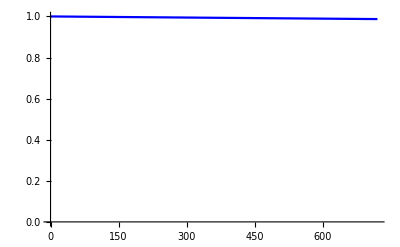

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

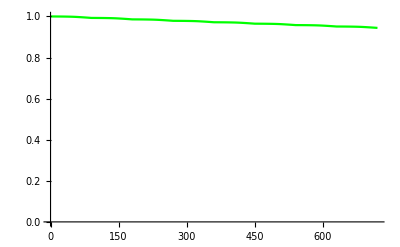

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

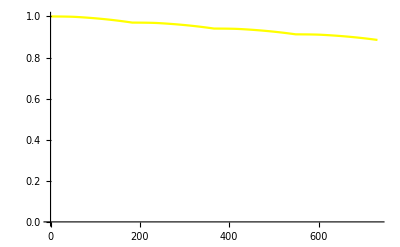

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

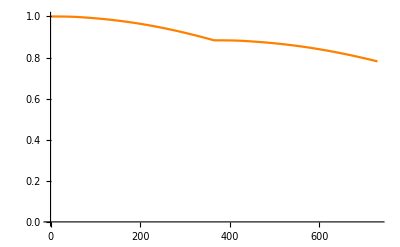

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

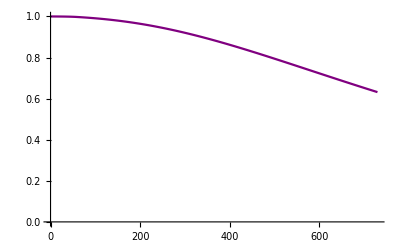

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

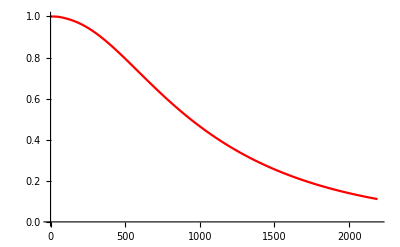

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

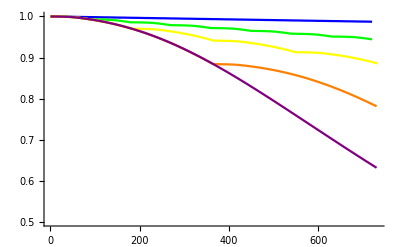

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/no_rtx_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/no_rtx_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.368299,0.218689,0.114345,0.0557105,0.0128374].

Show[0.368299,0.218689,0.114345,0.0557105,0.0128374]

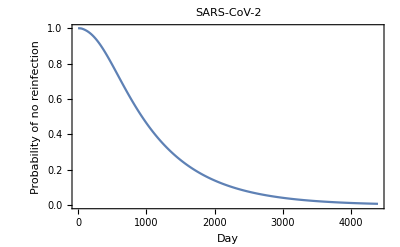

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{237.19,7.90633,0.649835}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{937.686,31.2562,2.569}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2848.55,94.9518,7.80426}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

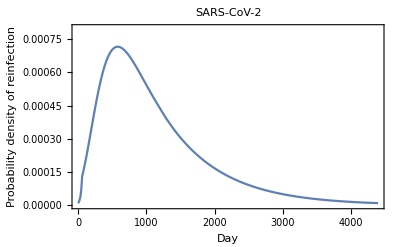

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed